```mathematica
Clear["Global`*"]
```

```mathematica
(* Mean frequencies of good individuals *)
z=1-x-y;
gxgood=(1-gx)*ϵ;
gxbad=gx*(1-ϵ);
gygood=(1-gy)*e;
gybad=gy*(1-e);
gzgood=x*(1-gz)*(gx*ϵ+(1-gx)*e)+y*(1-gz)*(gy*ϵ+(1-gy)*e)+z*(1-gz)*(gz*ϵ+(1-gz)*e);
gzbad=x*gz*(gx*(1-ϵ)+(1-gx)*(1-e))+y*gz*(gy*(1-ϵ)+(1-gy)*(1-e))+z*gz*(gz*(1-ϵ)+(1-gz)*(1-e));
gx=gx/.Solve[gxgood==gxbad,gx][[1]];
gy=gy/.Solve[gygood==gybad,gy][[1]];
gz=gz/.Solve[gzgood==gzbad,gz][[1]];
(*g=fx*gx+fy*gy+fz*gz;
g2=fx*gx^2+fy*gy^2+fz*gz^2;
b2=1-2*g+g2;
d2=g-g2;
ϵ=(1-e1)*(1-e2)+e1*e2;*)
```

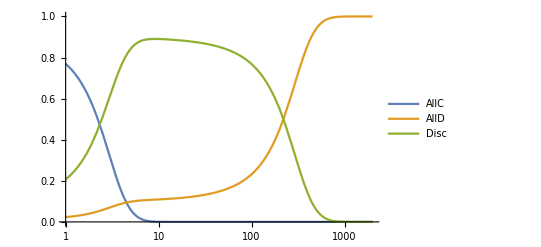

```mathematica
(* Plot numerical solutions *)
e=0.01;
ϵ=0.01;
r=3;
gz=0.01;
g=x[t]*gx+y[t]*gy+(1-x[t]-y[t])*gz;
Px=r*(x[t]+(1-x[t]-y[t])*gx)-1;
Py=r*(x[t]+(1-x[t]-y[t])*gy);
Pz=r*(x[t]+(1-x[t]-y[t])*gz)-g;
Pbar=x[t]*Px+y[t]*Py+(1-x[t]-y[t])*Pz;
sol=NDSolve[{x'[t]==x[t]*(Px-Pbar),y'[t]==y[t]*(Py-Pbar),x[0]==0.9,y[0]==0.01},{x,y},{t,1,2000}];
LogLinearPlot[Evaluate[{x[t],y[t],1-x[t]-y[t]}/.sol],{t,1,2000},PlotLegends->{"AllC","AllD","Disc"}]
```

```mathematica
(* Mean frequencies of good individuals *)
Gx=Solve[gx==g*ϵ+(1-g)*(1-ϵ)/.{g->fx*Gx+fy*gy+fz*gz},gx]
gy=Solve[gy==g*e2+(1-g)*(1-e2)/.{g->fx*gx+fy*gy+fz*gz},gy];
gz=E*(g*ϵ+(1-g)*(1-e2))+(1-E)*(g2*ϵ+d2*(e2+1-ϵ)+b2*(1-e2));
```

```mathematica
(* Expected payoffs *)
Πx = b*(fx+fz*gx)*(1-e1)-c*(1-e1);
Πy = b*(fx+fz*gx)*(1-e1);
Πz = b*(fx+fz*gx)*(1-e1)-c*g*(1-e1);
```

```mathematica
(* Vector field *)
VF={fx*(Πx-fx*Πx-fy*Πy-fz*Πz),fy*(Πy-fx*Πx-fy*Πy-fz*Πz),fz*(Πz-fx*Πx-fy*Πy-fz*Πz)};
```

```mathematica
(* Parameters *)
params={b->5,c->1,e1->0.02,e2->0.02,E->0.5};
```